```mathematica
f[x_] = x(1-x) - h x/(a+x);
D[f[x],x]
D[f[x],x]/.x->0
```

1-2 x+(h x)/(a+x)^2-h/(a+x)

1-h/a

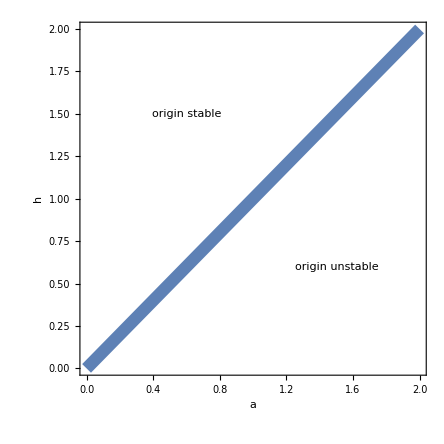

```mathematica
Show[ContourPlot[1-h/a==0,{a,0,2},{h,0,2},FrameLabel->{a,h},ContourStyle->{Thickness[0.02]},LabelStyle->Large],Graphics[Text[Style["origin stable",Large],{0.6,1.5}]],Graphics[Text[Style["origin unstable",Large],{1.5,0.6}]]]
Manipulate[Plot[{1-x, h /(a+x)},{x,0,1},PlotRange->{{0,1},{0,2}}],{h,0.1,2},{a,0,2}]
```

```mathematica
Manipulate[Plot[{1-x, h /(a+x)},{x,0,1},PlotRange->{{0,1},{0,2}},AxesLabel->{x,"function"},LabelStyle->Large,PlotStyle->Thickness[0.02]],{h,0.1,2},{a,0,2}]
```

Find the tangency.

```mathematica
expr = D[h/(a+x),x]
Solve[{expr==-1,1-x== h /(a+x)},{h,x}]
```

-h/(a+x)^2

{{h→1/4 (1+a)^2,x→(1-a)/2}}

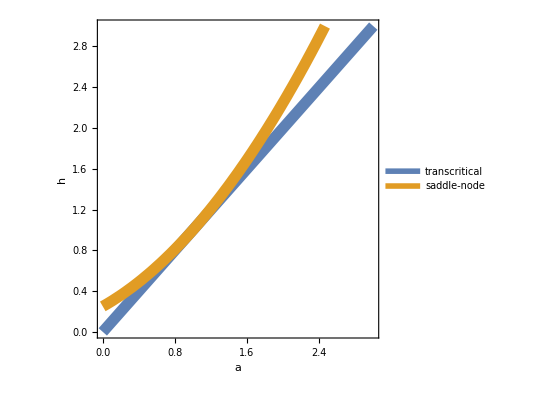

```mathematica
Show[ContourPlot[{1-h/a==0,h==1/4 (1+a)^2},{a,0,3},{h,0,3},FrameLabel->{a,h},ContourStyle->{Thickness[0.02]},LabelStyle->Large,PlotLegends->{"transcritical","saddle-node"}]]
```

Look at the bifurcation diagram for different values of h.

```mathematica
Manipulate[ContourPlot[{Piecewise[{{f[x],f'[x]<0}/.h->h0},Indeterminate]==0,Piecewise[{{f[x],f'[x]>0}/.h->h0},Indeterminate]==0},{a,0,3},{x,-0.05,1.5},ContourStyle->{Thickness[0.01],{Thickness[0.01],Dashed}},Frame->None,Axes->True,AxesLabel->{a,x},LabelStyle->Large],{h0,0.1,3}]
```

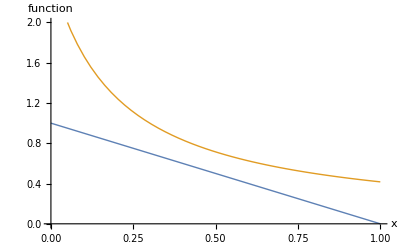

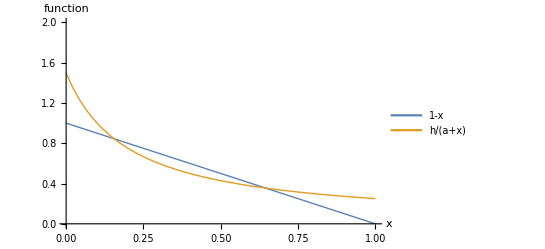

C06bistabilitycurves1.jpg

C06bistabilitycurves2.jpg

```mathematica
p0 = Plot[{1-x, 0.5 /(0.2+x)},{x,0,1},PlotRange->{{0,1},{0,2}},AxesLabel->{x,"function"},LabelStyle->Large,PlotStyle->Thick]
p1 = Plot[{1-x, 0.3 /(0.2+x)},{x,0,1},PlotRange->{{0,1},{0,2}},AxesLabel->{x,"function"},LabelStyle->Large,PlotStyle->Thick,PlotLegends->Placed[{"1-x","h/(a+x)"},{0.6,0.8}]]
Export["C06bistabilitycurves1.jpg",p0]
Export["C06bistabilitycurves2.jpg",p1]
```

```mathematica
GraphicsGrid[{{p0,p1}}]
```

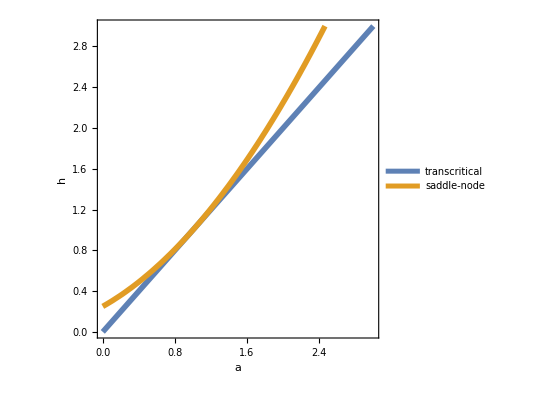

C06bistabilitybifn.jpg

```mathematica
p3 = Show[ContourPlot[{1-h/a==0,h==1/4 (1+a)^2},{a,0,3},{h,0,3},FrameLabel->{a,h},ContourStyle->{Thickness[0.01]},LabelStyle->Large,PlotLegends->{"transcritical","saddle-node"}]]
Export["C06bistabilitybifn.jpg",p3]
```